# Critical genome size B_c : heuristic approximation

Run the cell below to get the heuristic approximations for Bc as a function of the parameters: Bc = Bc(“Floor” or “Ceiling”, N, μ, qmin)

```mathematica
(*************Using 'floor' function when calculating "transition time"************)
Bc["Floor",n0_,μ0_,qmin0_]:=Module[{n=n0,qmin=qmin0,μ=μ0,q1,q2,σ2,c,B,τ},
qeq=1/(n Exp[4μ]-n+1);
τ=Floor[Log[(qmin-qeq)/(1-qeq)]/Log[(1-1/n)Exp[-4μ]]];
If[Not@RealValuedNumberQ[τ],Return[]];
q1=1;
q2=1;
σ2=0;
c=0;
Do[
q1novo=Simplify[Exp[-4μ](1/n+(1-1/n)q1)];
q2novo=Simplify[(Exp[-8μ])((3/n^2-2/n^3)+(1-1/n)(6/n-8/n^2)q1+(1-1/n)(1-2/n)(1-3/n)q2)];
σ2novo=Simplify[(Exp[-8μ](n-2)^2/(4n^2(n-1)))((1-q1)^2+(n^2+2n-2)σ2(1-2/(n(n-1)))/n+2(n^2-6n+4)(1-2/(n(n-1)))c/n)+1/B-(Exp[-8μ]/(4B))(1+2/(n(n-1))+2q1+4(n-2)q1/(n(n-1))+(n-2)(n-3)q2/(n(n-1)))];
cnovo=Simplify[(Exp[-8μ]/(2n^2))(σ2(1-2/(n(n-1)))(n-4+4/n)+c(1-2/(n(n-1)))(n^2-8n+20-16/n))+(Exp[-4μ]/(B*n^2))(n+n(n-1)q1)-(Exp[-8μ]/(2B*n^2))((n+2)+(n^2+4n-8)q1+(n-2)(n-3)q2)];
q1=q1novo;
q2=q2novo;
σ2=σ2novo;
c=cnovo
,{t,1,τ}];
Λ1=Limit[σ2,B->∞];
Λ2=Limit[B*σ2,B->0];
k=1;
δq=(qmin/qeq-1)/(n Exp[4μ](k-1)+(n-1));
Λ2/((δq+Sqrt[Λ1])^2-Λ1)
]

(*************Using 'ceiling' function when calculating "transition time"************)
Bc["Ceiling",n0_,μ0_,qmin0_]:=Module[{n=n0,qmin=qmin0,μ=μ0,q1,q2,σ2,c,B,τ},
qeq=1/(n Exp[4μ]-n+1);
τ=Ceiling[Log[(qmin-qeq)/(1-qeq)]/Log[(1-1/n)Exp[-4μ]]];
If[Not@RealValuedNumberQ[τ],Return[]];
q1=1;
q2=1;
σ2=0;
c=0;
Do[
q1novo=Simplify[Exp[-4μ](1/n+(1-1/n)q1)];
q2novo=Simplify[(Exp[-8μ])((3/n^2-2/n^3)+(1-1/n)(6/n-8/n^2)q1+(1-1/n)(1-2/n)(1-3/n)q2)];
σ2novo=Simplify[(Exp[-8μ](n-2)^2/(4n^2(n-1)))((1-q1)^2+(n^2+2n-2)σ2(1-2/(n(n-1)))/n+2(n^2-6n+4)(1-2/(n(n-1)))c/n)+1/B-(Exp[-8μ]/(4B))(1+2/(n(n-1))+2q1+4(n-2)q1/(n(n-1))+(n-2)(n-3)q2/(n(n-1)))];
cnovo=Simplify[(Exp[-8μ]/(2n^2))(σ2(1-2/(n(n-1)))(n-4+4/n)+c(1-2/(n(n-1)))(n^2-8n+20-16/n))+(Exp[-4μ]/(B*n^2))(n+n(n-1)q1)-(Exp[-8μ]/(2B*n^2))((n+2)+(n^2+4n-8)q1+(n-2)(n-3)q2)];
q1=q1novo;
q2=q2novo;
σ2=σ2novo;
c=cnovo
,{t,1,τ}];
Λ1=Limit[σ2,B->∞];
Λ2=Limit[B*σ2,B->0];
k=1;
δq=(qmin/qeq-1)/(n Exp[4μ](k-1)+(n-1));
Λ2/((δq+Sqrt[Λ1])^2-Λ1)
]
(*****************************************************************************)
```

For example:

```mathematica
Bc["Floor",1000,0.001,0.8]
```

11295.6

```mathematica
Bc["Ceiling",200,0.005,0.75]
```

922.633

## Some Images

### Bc as a function of μ for different qmin and N fixed

```mathematica
(*Calculating Bc*)
n=1000;
qminList={0.75,0.8,0.85,0.9,0.95};
Print@Dynamic@μ
Print@Dynamic@qmin
Do[
solutionμFloor[qmin]={};
solutionμCeili[qmin]={};
Do[
AppendTo[solutionμFloor[qmin],{μ,Bc["Floor",n,μ,qmin]}];
AppendTo[solutionμCeili[qmin],{μ,Bc["Ceiling",n,μ,qmin]}]
,{μ,0.0002,0.005,0.0001}]
,{qmin,qminList}]
```

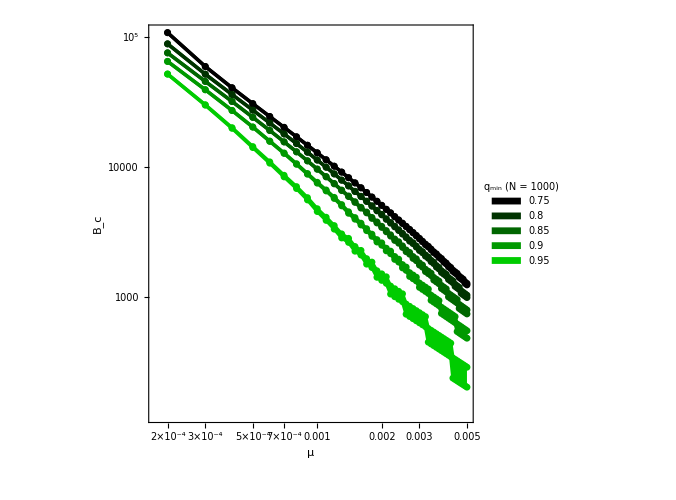

```mathematica
(*Image*)
Plotμ=ListPlot[Join[Table[solutionμFloor[qmin],{qmin,qminList}],Table[solutionμCeili[qmin],{qmin,qminList}]],
PlotRange->All,
ImageSize->500,
ImagePadding->{{100,20},{80,10}},
Joined->True,
Mesh->All,
PlotStyle->Table[{RGBColor[0,(i-1)/Length[qminList],0],Thickness[0.005],PointSize->0.01},{i,1,Length@qminList}],
Filling->Table[i->{i+Length[qminList]},{i,1,Length@qminList}],
FillingStyle->Directive[Thickness[0.0075],Opacity[1]],
ScalingFunctions->{"Log","Log"},
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{"μ","B_c"},
PlotLegends->Placed[SwatchLegend[Table[RGBColor[0,(i-1)/Length[qminList],0],{i,1,Length@qminList}],qminList,LegendLabel->"q_min\n(N = 1000)",LabelStyle->Directive[Black,FontSize->16]],{0.12,0.23}],
AspectRatio->1./1
]
```

### Bc as a function of N for different μ and qmin fixed

```mathematica
(*Calculating Bc*)
qmin=0.8;
μList={0.0001,0.0002,0.0003,0.0004,0.0005};
Print@Dynamic@μ
Print@Dynamic@n
Do[
solutionNFloor[μ]={};
solutionNCeili[μ]={};
Do[
AppendTo[solutionNFloor[μ],{n,Bc["Floor",n,μ,qmin]}];
AppendTo[solutionNCeili[μ],{n,Bc["Ceiling",n,μ,qmin]}]
,{n,400,10000,200}]
,{μ,μList}]
```

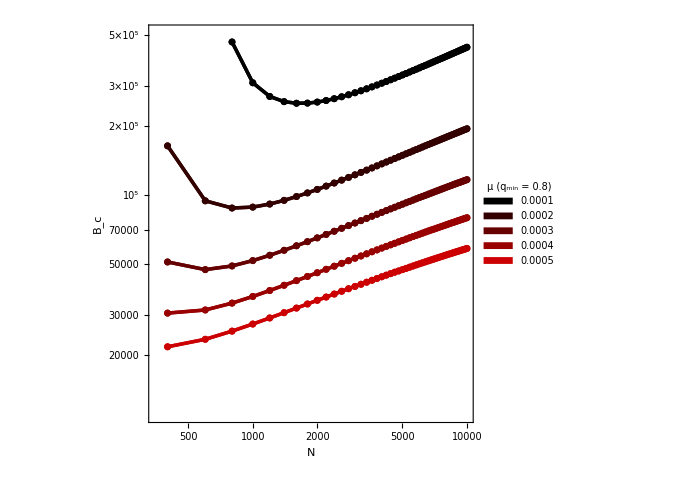

```mathematica
(*Image*)
Plotn=ListPlot[Join[Table[solutionNFloor[μ],{μ,μList}],Table[solutionNCeili[μ],{μ,μList}]],
PlotRange->{1.1 10^4,5.1 10^5},
ImageSize->500,
ImagePadding->{{100,20},{80,10}},
Joined->True,
Mesh->All,
PlotStyle->Table[{RGBColor[(i-1)/Length[μList],0,0],Thickness[0.005],PointSize->0.01},{i,1,Length@μList}],
Filling->Table[i->{i+Length[μList]},{i,1,Length@μList}],
FillingStyle->Directive[Thickness[0.0075],Opacity[1]],
ScalingFunctions->{"Log","Log"},
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{"N","B_c"},
PlotLegends->Placed[SwatchLegend[Table[RGBColor[(i-1)/Length[μList],0,0],{i,1,Length@μList}],μList,LegendLabel->"μ\n(q_min = 0.8)",LabelStyle->Directive[Black,FontSize->16]],{0.88,0.23}],
AspectRatio->1/1
]
```